## Setup

```mathematica
Clear["Global`*"];
```

```mathematica
LaunchKernels[6];
```

## Calculate T with forward difference method

### Manually integrate Schrodinger’s equation

The grid of x points in the region of the support of the potential

```mathematica
xgrid[p_]:=Module[{a,b,n,m, step,xs},
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
step = (b-a)/(n);

xs = Table[x,{x,a,b,step}]//N;

Return[xs];
]
```

The grid of x points in the entire region including some to the left of the support of the potential for determining the value of T.

```mathematica
xgridFull[p_]:=Module[{a,b,n,m, step,xs},
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
step = (b-a)/(n);

xs = Table[x,{x,a-m*step,b,step}]//N;

Return[xs];
]
```

```mathematica
yvec[k_,p_]:=Module[{a,b,n,m, step,y},
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
step = (b-a)/(n-1);

y =SparseArray[
{n+m-1->1,
n+m->(-4+Exp[I*k*step]),
n+m+1->(5-4*Exp[I*k*step]+Exp[2*I*k*step])
}, 
{n+m+1}];

Return[y];
]
```

```mathematica
yvecKVec[kVec_,p_]:=Table[yvec[k,p],{k,kVec}]
```

```mathematica
D2Matrix[p_]:= Module[{xg, a,b,n,m, step, diag, u1, u2,u3, mat},
xg=xgrid[p];
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
step = (b-a)/(n-1);

(*Some of these elements are constant and should not be recreated for every solution *)
diag = Band[{1,1}]->2;
u1 = Band[{1,2}]->-5;
u2=Band[{1,3}]->4;
u3=Band[{1,4}]->-1;
mat = SparseArray[{diag,u1,u2,u3},{1+n+m, 1+n+m}];

Return[mat]
];
```

```mathematica
EMatrix[k_,p_]:=Module[{ a,b,n,m, step, diag, mat},
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
step = (b-a)/(n-1);

(*Some of these elements are constant and should not be recreated for every solution *)
diag = Band[{1,1}]->step^2*k^2;
mat = SparseArray[{diag},{1+n+m, 1+n+m}];

Return[mat];
];
```

```mathematica
EMatrixKVec[kVec_,p_]:=Table[EMatrix[k,p],{k,kVec}]
```

```mathematica
VMatrix[V_,p_]:=Module[{xg, a,b,n,m, step, u1V, matV},
xg=xgrid[p];
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
step = (b-a)/(n-1);

(*These elements are constant for every value of k and should only be generated once per k value*)
u1V=Band[{m+1,m+1}]->2*step^2*V[xg];
matV = SparseArray[u1V,{1+n+m,1+n+m}];

Return[Association["xgrid"->xg, "V"->matV]];
];
```

```mathematica
kGrid[p_]:=Module[{kmin,kmax,numk,kstep},
kmin=p["kmin"];
kmax=p["kmax"];
numk = p["numk"];
kstep = (kmax-kmin)/(numk-1);

Return[Table[k,{k,kmin,kmax,kstep}]];
];
```

```mathematica
psiSolutionKVec[V_,kVec_,p_,D2_,EMatrixVector_,yVector_]:=Module[{VDict, xg,VV, soln},
VDict = VMatrix[V,p];
xg=VDict["xgrid"];
VV=VDict["V"];

soln = Table[{
kVec[[i]],
LinearSolve[D2-VV+EMatrixVector[[i]], yVector[[i]]]
},{i,1, Length[kVec]}];
Return[soln];
];
```

```mathematica
psiSolutionKVecBindXGrid[V_,kVec_,p_,D2_,EMatrixVector_,yVector_]:=Module[{VDict, xgfull,VV, soln},
VDict = VMatrix[V,p];
xgfull=xgridFull[p];
VV=VDict["V"];

soln = Table[{
kVec[[i]],
Transpose[{xgridFull[p],LinearSolve[D2-VV+EMatrixVector[[i]], yVector[[i]]]}]
},{i,1, Length[kVec]}];
Return[soln];
];
```

### Test with sech^2 potential

```mathematica
V[x_]:=1/Cosh[x]^2;
params = Association["a"->-10, "b"->10,"n"->500,"m"->20,"kmin"->0.01,"kmax"->2.001,"numk"->100];
kgrid = kGrid[params];
```

```mathematica
d2mat = D2Matrix[params];
emat=EMatrixKVec[kgrid,params];
yyvec=yvecKVec[kgrid,params];
```

```mathematica
psiSol=psiSolutionKVecBindXGrid[V,kgrid,params,d2mat,emat,yyvec];
```

```mathematica
probabilities=Table[{ksol[[1]],Table[{xpsi[[1]],Abs[xpsi[[2]]]^2},{xpsi, ksol[[2]]}]},{ksol,psiSol}];
```

```mathematica
pltProbabilities[kindex_]:=ListPlot[{probabilities[[kindex,2]]},GridLines->Automatic,PlotLabel->"k="<>(probabilities[[kindex,1]]//ToString)]
```

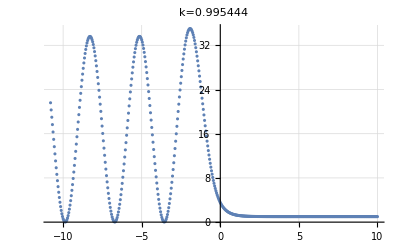

```mathematica
pltProbabilities[50]
```

#### Timing for 10,000 schrod solutions:

```mathematica
timingSolutions=Table[psiSolutionKVec[V,kgrid,params,d2mat,emat,yyvec],{i,1,100}]//Timing; (*100 solutions per iteration x 100 iterations = 10000 solutions*)
```

```mathematica
timingSolutions[[1]] (*More than four times as fast as NDSolve but also doing more*)
```

2.7136

here, timing is proportional to n+m ~ n